2.16699

| Interno   | Esterno

Draw

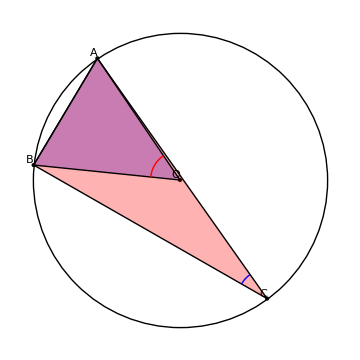

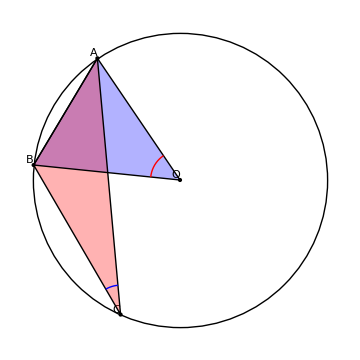

```mathematica
circleCenter={0,0};
alpha=Which[input==180,0°,True,Mod[input,180]°]/.input->50;

AAngle=RandomReal[{0,Pi}]
circAngle=RandomReal[{alpha+0.1,2*Pi-0.1}];
points={CirclePoints[{1,AAngle},1][[1]]};
AppendTo[points,RotationMatrix[alpha].points[[1]]];
beta=180°-alpha;
choices={ RandomChoice[{-1, 1}] *(alpha/2 + 0.1+RandomReal[{0, beta  - 0.1}]),alpha/2 + beta +RandomReal[{0, alpha}]};
RadioButtonBar[Dynamic[choice], {2 -> "Interno",  1 -> "Esterno"}]
drawF[c_]:=Module[{pointsS},
pointsS=Append[points,RotationMatrix[choices[[c]]].middlePoint/.middlePoint->RotationMatrix[alpha/2].points[[1]]];
pointsS
]
drawF[choice];
Button["Draw",
Print
[Graphics[{
Circle[circleCenter, 1] ,
Point[circleCenter],
Point /@ drawF[choice],

{Opacity[0.3],Style[Triangle[{drawF[choice][[1]],drawF[choice][[2]],circleCenter}], Blue]},
{Opacity[0.3],Style[Triangle[drawF[choice]], Red]},

Line[Append[drawF[choice],  drawF[choice][[1]]]],(* triangolo con angolo al centro *)
Line[{drawF[choice][[1]],drawF[choice][[2]],circleCenter, drawF[choice][[1]]}], (* triangolo con angolo alla circonferenza *)

Tooltip[Style[Circle[circleCenter, 0.2, {AAngle, AAngle + alpha}], Red, Thick ], alpha],
Tooltip[Style[Circle[drawF[choice][[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2],
(* Annotation[Style[Circle[drawF[choice][[3]], 0.2, {angletemp, angletemp+alpha/2}], Blue, Thick ], alpha/2, "Mouse"], *)

MapIndexed[ Text[FromCharacterCode[#2[[1]]+ 64] , #1, {1.5,-1.5}]&, drawF[choice]], 
Text["O", circleCenter,{1.5,-1.5}]
}, ImageSize -> Medium]/.angletemp -> PlanarAngle[drawF[choice][[3]] -> { {drawF[choice][[3]][[1]] + 1, drawF[choice][[3]][[2]]}, drawF[choice][[1]]}]
]]
```